Author: C. Moreira
Institution: School of Information Systems, Queensland University of Technology
Date of Last version: 19 / 04 / 2020

```mathematica
(* Install MaTeX *)
```

```mathematica
Needs["MATLink`"]
```

```mathematica
(* Load MaTEX *)
```

```mathematica
<<MaTeX`
```

```mathematica
(* Load auxiliary functions *)
```

```mathematica
z0:=0; y0:=0; x0:=0; c:=1; b:=1; a:=1;
F[x_,y_]:=(a x0+b y0+c z0);
```

```mathematica
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
PartialTrace[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])
```

```mathematica
(* Return the off-diagonal of a density matrix *)
```

```mathematica
AntiDiagonal[m_]:=Diagonal[m[[-1;;1;;-1,1;;-1;;1]]]
```

# Quantum-Like Bayesian Networks for Violations of the Sure Thing Principle and More

## Introduction

The model proposed in this work is founded on probabilistic graphical models, namely on Bayesian networks, which are one of the most powerful structures known by the Computer Science community for deriving probabilistic inferences (for instance, in medical diagnosis, spam filtering, image segmentation, etc) (Koller, 2009). The main advantage of these models is that they provide a link between probability theory and graph theory. And a fundamental property of graph theory is its modularity: one can build a complex system by combining smaller and simpler parts. Computationally, it is easier to combine different pieces of evidence and to perform probabilistic inferences, instead of calculating all possible events and their respective beliefs in massive full joint probability distributions (Griffiths, 2008). In the same way, Bayesian Networks represent the decision problem in small modules that can be combined to perform inferences (Pearl, 1988). Only the probabilities which are actually needed to perform the inferences are computed.

This process can also be viewed under the perspective of human cognition (Griffiths, 2008). During the inference process, the decision-makers cannot process all possible information of the decision problem, and consequently, they combine several smaller pieces of evidence (or information) together with uncertainty about the decision problem in order to reach a final decision (Pearl, 1988). This lack of information can be translated into the feelings of ambiguity, uncertainty, vagueness, risk, ignorance, etc (Zadeh, 2006), and they are a consequence of various factors, such as limitations in their ability to observe the world, limitations in their ability to model it and possibly even because of innate nondeterminism (Koller, 2009). 
-Graphics--Graphics-

Figure 1: Classical Bayesian Network                                                                                      	Figure 2: Quantum-Like Bayesian Network

Under a classical point of view, uncertainty is represented by classical probability theory, where the decision - maker is assumed to be experiencing a definite state in each time period.Under a quantum probabilistic perspective, this representation of uncertainty is different.When reasoning under uncertainty, the decision - maker is in an indefinite state, which results in a superposition of beliefs (Busemeyer & Bruza, 2012)}.A superposition can be generally understood as the simultaneous occurrence of all the beliefs that the decision - maker is experiencing in a single time frame.This superposition of beliefs will result in the occurrence of quantum interference effects that under high levels of uncertainty can disturb the decision - maker' s beliefs.One can look at quantum interference effects as waves that crash between each other, leading to waves (beliefs) that are destroyed (destructive interference) and waves that can be reinforced (constructive interference).This phenomena of quantum interference is also the core of quantum computation and the reason why such computers can achieve such high performances in terms of speed (Aaronson, 2013). Figure 2, shows an example of the role of quantum interference effects within unobserved nodes in Bayesian networks.

## Violations of the Sure Thing Principle in Cognitive Psychology Experiments

-Graphics-

-Graphics-

## Quantum-Like Bayesian Networks with Examples

Moreira & Wichert, (2014, 2016) proposed a quantum-like Bayesian network which extends Bayesian networks by replacing real valued probabilities by complex quantum probability amplitudes.

A quantum-like Bayesian network (QLBN) can be defined by a pair ⟨𝒢, ρ_𝒢⟩, where,

𝒢 is a directed acyclic graph represented by a pair 𝒢 = (V, E). Each vertex v_i∈ V  is a random variable represented by a quantum state in a complex Hilbert space H ∈ 𝒢 and e_j ∈ E is a set of directed edges expressing relationships between vertices (Leifer, 2008).

ρ_𝒢 is a density operator is a composite state of independent complex Hilbert spaces of different dimensions. A Hilbert space can be defined as a generalisation and extension of the Euclidean space into spaces with any finite or infinite number of dimensions. It is a vector space of complex numbers and offers the structure of an inner product to enable the measurement of angles and lengths (Mika 2003). The system ρ_𝒢 is defined over a fixed basis and therefore it satisfies the same conditional independence constraints as in a classical Bayesian network (Leifer, 2008).

The next sections formalize the main elements of QLBNs by means of the Dirac notation presents the basic elements of this notation for the reader who is not familiar with it).

#### Example of a Quantum-Like Bayesian Network and a Bayesian Network for Shafir & Tversky (1992) Experiment

-Graphics-

```mathematica
(* Cleaning all variables in memory *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(* Specify the overall statistics of the experiment (values taken from tables 1 and 2) *)
pdd=0.97;          (* probability of P2 defecting, given P1 also defected *)
pcd = 0.84;        (* probability of P2 defecting, given that P1 cooperated *)
pdc = 1-pdd;    (* probability of P2 coorepating, given P1 defected *)
pcc=1-pcd;    (* probability of P2 cooperating given P1 cooperated *)
```

```mathematica
prior = 0.5;   (* we assume neutral priors in this expriment, which means the player has a belief that the opponent has a 50% chance of either Defecting or cooprating *)
```

#### State Space

Let  H ∈ 𝒢 be a complex Hilbert space that represents a quantum - like Bayesian network.
Let H_1∈ H_𝒢, H_2∈ H_𝒢,... , H_n∈ H_𝒢 be a set of different Hilbert spaces that makes up the QLBN, then the Hilbert space H_𝒢 that represents the network is defined as the tensor product of each individual Hilbert space : H_𝒢 = H_1 ⊗ H_2⊗...⊗ H_n. The dimension of H_𝒢corresponds to the size of the full joint probability distribution.

#### Quantum States

The random variables that make up the network are represented as quantum states.This means that random variables are represented as a probability distribution of complex probability amplitudes over the different outcomes that the random variable can have, instead of being specified as real numbers (like in the traditional Bayesian network).In quantum - like Bayesian networks, one also needs to distinguish between two types of quantum states : (1) states corresponding to root nodes, and (2) states corresponding to child nodes.

Root nodes correspond to quantum pure states.

An example of a quantum pure state is given by Player 1 in Shafir and Tversky (1992) experiment.

|BeliefP1 ⟩ = α_1 e^ⅈθ_1|Def ⟩ + α_2 e^ⅈθ_2|Coop ⟩

where |Def ⟩ and |Coop ⟩ correspond to the 0 / 1 basis, α_i ∈ ℝ and θ_i ∈ ℝis the phase of amplitude α_i
|Def ⟩ = |0 ⟩ = (1
0) and |Coop ⟩ = |1 ⟩ = (0
1)

```mathematica
Needs["Quantum`Notation`"]
```

```mathematica
(* ########################### DEFINING PURE QUANTUM STATES ######################################## *)
(* Each parent node of the network corresponds to a Quantum Pure State *)
(* |BeliefP1 ⟩ corresponds to the belief that Player 1 will either defect with some probability *prior* or cooperate with some probability *1-prior* *)
(* In these experiments, we consider that the player has an equal chance if either defecting or cooperating *)
```

```mathematica
BeliefP1 =({{Sqrt[prior ] ⅇ^(ⅈ Re[θ1])}, {Sqrt[(1-prior) ] ⅇ^(ⅈ Re[θ2])}})
```

{{0.5 ⅇ^(2 ⅈ Re[θ1])},{0.5 ⅇ^(2 ⅈ Re[θ2])}}

```mathematica
(* --------------------------------------------------------------------------------------------------- *)
```

Child nodes represent a statistical distribution of different quantum states. This means that we  represent child nodes as an ensemble where the conditioned probabilities can be found in one of the different quantum states in the ensemble (McMahon, 2007). We make this more concrete by modeling Player 2 quantum state in Shafir & Tversky (1992) experiment.

Player 2 state is dependent on his beliefs regarding Player 1’s actions. If P2 believes that Player 1 will defect, then

|P2 |  BeliefP1 = Def⟩ = β_11 e^ⅈθ_3|Def ⟩ + β_12 e^ⅈθ_4|Coop ⟩

And  if P2 believes that Player 1 will defect, then

|P2 |  BeliefP1 = Coop⟩ =  β_21 e^ⅈθ_3|Def ⟩ + β_22 e^ⅈθ_4|Coop ⟩

So, Player 2 state will be an ensemble comprising the states |P2 |  BeliefP1 = Def⟩ and |P2 |  BeliefP1 = Coop⟩:

|P2 |  BeliefP1 ⟩  = ( β_11 ⅇ^(ⅈ Re[θ3]) |  β_12 ⅇ^(ⅈ Re[θ4])
  β_21 ⅇ^(ⅈ Re[θ5]) |   β_22 ⅇ^(ⅈ Re[θ6]))

This means that the params β_i and γ_i will have the following interpretations:

β_1 and β_2 corresponds to the complex amplitude of the experimental probabilities Pr( P2 = Def | Belief_P1 = Def ) = √pdd and Pr( P2 = Def | Belief_P1 = Coop ) = √pcd, respectively

γ_1 and γ_2 corresponds to the experimental probabilities Pr( P2 = Coop | Belief_P1 = Def ) = √(1-pdd) and Pr( P2 = Coop | Belief_P1 = Coop ) = √(1-pcd), respectively

```mathematica
(* ####################### DEFINING AN ENSEMBLE OF QUANTUM STATES ################################## *)
```

```mathematica
(* Define the Quantum Conditional Probability States |X2X1d⟩, |X2X1c⟩. Each state is defined in its own Hilbert Space *)
```

```mathematica
(*|P2BeliefP1⟩: Player 2 Prob. Amplitudes, given Player 1 is believed to have chosen Defect   *)
(*|P2BeliefP1⟩: Player 2 Prob. Amplitudes given Player 1 is believed to have chosen Cooperate *)
```

```mathematica
P2BeliefP1=({{Sqrt[pdd] ⅇ^(ⅈ Re[θ3]), Sqrt[pcd] ⅇ^(ⅈ Re[θ4])}, {Sqrt[pdc] ⅇ^(ⅈ Re[θ5]), Sqrt[pcc] ⅇ^(ⅈ Re[θ6])}});
```

```mathematica
MatrixForm[P2BeliefP1]
```

(ⅇ^(ⅈ Re[θ3]) √pdd | ⅇ^(ⅈ Re[θ4]) √pcd
ⅇ^(ⅈ Re[θ5]) √pdc | ⅇ^(ⅈ Re[θ6]) √pcc)

```mathematica
(* Visualise the impact of the probability amplitudes *)
```

```mathematica
data1 = Table[Sqrt[pdd]Exp[ⅈ θ], {θ,0,2π,0.0001}];
```

```mathematica
data2 = Table[Sqrt[pcd]Exp[ⅈ θ], {θ,0,2π,0.0001}];
```

```mathematica
data3 = Table[Sqrt[pdc]Exp[ⅈ θ], {θ,0,2π,0.0001}];
```

```mathematica
data4 = Table[Sqrt[pcc]Exp[ⅈ θ], {θ,0,2π,0.0001}];
```

```mathematica
ComplexListPlot[{data1, data2, data3, data4},PlotLegends->{"|P2=Def|BeliefP1=Def⟩","|P2=Def|BeliefP1=Coop⟩","|P2=Coop|BeliefP1=Def⟩","|P2=Coop|BeliefP1=Coop⟩"}]
```

-Graphics-

```mathematica
plot1 = ListPlot[{Im[data1], Im[data3]},PlotLegends->{"|P2=Def|BeliefP1=Def⟩","|P2=Coop|BeliefP1=Def⟩"},AxesLabel->Automatic];
```

```mathematica
plot2 = ListPlot[{Im[data2], Im[data4]},PlotLegends->{"|P2=Coop|BeliefP1=Def⟩","|P2=Coop|BeliefP1=Coop⟩"}];
```

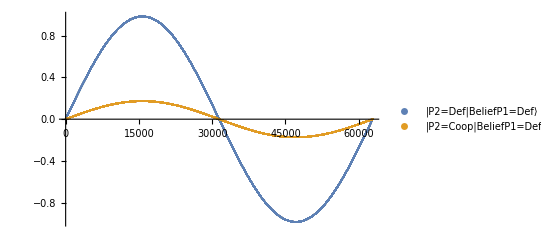
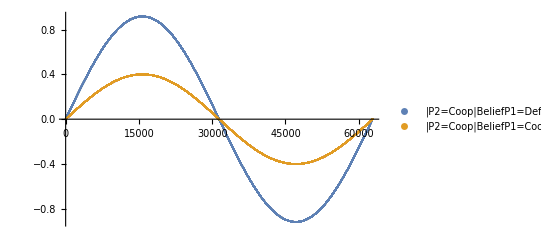

```mathematica
{plot1, plot2}
```

```mathematica
(* --------------------------------------------------------------------------------------------------- *)
```

#### Create Quantum Superposition State of the Network

In quantum theory, all individual quantum states contained in a Hilbert Space are defined by a superposition state which is represented by a quantum state vector |S_𝒢⟩  comprising the occurrence of all events of the system.This can be analogous to the classical full joint probability distribution, with the difference that instead of using real numbers to express probabilities, one uses complex probability amplitudes.
The superposition state  |S_𝒢⟩  comprising all possible events in Hilbert space  |H_𝒢⟩  is given by

|S_𝒢⟩ = ∑_(_(k_1...,k_n)) ∏_(j∈ 𝒢) ψ(X=j)|Pa(ψ(X=j)) |k_1⟩⊗|k_2⟩ ⊗...⊗ |k_n⟩,

where k_1,k_2,...,k_n  corresponds to the basis of each quantum state in the network.

For the specific example of Shafir & Tversky (1992), this superposition state is given by:

|S_𝒢⟩= ∑_(i=1)^2 (∑_(j=1)^2)^□α_i β_ij|BeliefP1 = i⟩⊗|P2 = j ⟩

|S_𝒢⟩= α_1 β_11|Def⟩⊗|Def ⟩+α_1 β_12|Def⟩⊗|Coop ⟩+α_2 β_21|Coop⟩⊗|Def ⟩+α_2 β_22|Coop⟩⊗|Coop ⟩

|S_𝒢⟩=      √(prior pdd)ⅇ^(ⅈ Re[θ1]+ⅈ Re[θ3])|Def Def ⟩+
√(prior pdc)ⅇ^(ⅈ Re[θ1]+ⅈ Re[θ5])|DefCoop ⟩+
       √(prior pcd)ⅇ^(ⅈ Re[θ2]+ⅈ Re[θ4])|CoopDef ⟩+
              √(prior pcc)ⅇ^(ⅈ Re[θ2]+ⅈ Re[θ6])|CoopCoop ⟩

```mathematica
(* ######### COMPUTE THE SUPERPOSITION STATE FROM THE JOINT PROBABILITY DISTRIBUTION ######### *)
(* The goal is to create a quantum density matrix that corresponds to the product of the factors of the quantum states that represent the random variables of the QBN*)
```

```mathematica
S=ConstantArray[0,{4}];
For[c=1;i=1,i≤2,i++,
For[j=1,j≤2,j++,
S[[c]]=BeliefP1[[i]] P2BeliefP1[[j,i]];
c=c+1;
]];
```

```mathematica
MatrixForm[S]
```

(0.696419 ⅇ^(ⅈ Re[θ1]+ⅈ Re[θ3])
0.122474 ⅇ^(ⅈ Re[θ1]+ⅈ Re[θ5])
0.648074 ⅇ^(ⅈ Re[θ2]+ⅈ Re[θ4])
0.282843 ⅇ^(ⅈ Re[θ2]+ⅈ Re[θ6]))

```mathematica
S=({{0.696419413859206 ⅇ^(ⅈ Re[θ1])}, {0.12247448713915897 ⅇ^(ⅈ Re[θ2])}, {0.6480740698407861 ⅇ^(ⅈ Re[θ3])}, {0.28284271247461906 ⅇ^(ⅈ Re[θ4])}});
```

#### Compute Density Matrix

The density operator, ρ_𝒢, aims to describe a system where we can compute the probabilities of finding each state in the network.One way to achieve this is by computing a density operator through the outer product of the superposition state of the composite system, S_𝒢 (McMahon, 2007).

ρ_𝒢=|S_𝒢⟩⟨S_𝒢|

The density operator also contains quantum interference terms in the off - diagonal elements, which are the core of this model.It is precisely through these off - diagonal elements that, during the inference process, one is able to obtain quantum interference effects, and consequently, deviations from normative probabilistic inferences.It follows that this model allows different levels of representations of decisions under uncertainty ranging from (1) fully rational and optimal decisions (fully classical) that follow the axioms of expected utility (connected to rational theories of choice in Economics) (von Neumann, 1953), (2) sub-optimal decisions that deviate from the predictions of expected utility theory, but still provide satisfying utilities to the decision - maker (connected to the theories of bounded rationality (Griffiths, 2008, Gigerenzer, 1996), to (3) irrational decisions (Tversky, 1992) ( fully quantum) that reflect the choice of decisions that lead to lower utilities (connected to paradoxical decisions and cognitive bias).Note that quantum interference effects are non - linear functions that can be mapped to the non - linear activation functions in neural networks (Grossberg, 1988).

```mathematica
ρ = FullSimplify[ExpandAll[S . ConjugateTranspose[S]]];
```

```mathematica
MatrixForm[ρ]
```

(0.485 | 0.0852936 ⅇ^(ⅈ Re[θ1-θ2]) | 0.451331 ⅇ^(ⅈ Re[θ1-θ3]) | 0.196977 ⅇ^(ⅈ Re[θ1-θ4])
0.0852936 ⅇ^(-ⅈ Re[θ1-θ2]) | 0.015 | 0.0793725 ⅇ^(ⅈ Re[θ2-θ3]) | 0.034641 ⅇ^(ⅈ Re[θ2-θ4])
0.451331 ⅇ^(-ⅈ Re[θ1-θ3]) | 0.0793725 ⅇ^(-ⅈ Re[θ2-θ3]) | 0.42 | 0.183303 ⅇ^(ⅈ Re[θ3-θ4])
0.196977 ⅇ^(-ⅈ Re[θ1-θ4]) | 0.034641 ⅇ^(-ⅈ Re[θ2-θ4]) | 0.183303 ⅇ^(-ⅈ Re[θ3-θ4]) | 0.08)

```mathematica
(* Check if calculations are correct. The classical full joint distribution should correspond to the sum of all diagonal elements of the density matrix *)
```

```mathematica
If[Total[Diagonal[ρ]] == 1,
Print[Correct!],
Print[Error! ]]
```

Correct!

#### Partial Trace of a System

To check player 1 marginal distribution:

Tr_B=(a11 | a12 | a13 | a14
a21 | a22 | a23 | a24
a31 | a32 | a33 | a34
a41 | a42 | a43 | a44) = (tr(a11 | a12
a21 | a22)
tr (a31 | a32
a41 | a42)  tr(a13 | a14
a23 | a24)
tr (a33 | a34
a43 | a44)) = (a11+a22 | a13+a24
a31+a42 | a33+a44)

To check player 2 marginal distribution:

Tr_A=(a11 | a12 | a13 | a14
a21 | a22 | a23 | a24
a31 | a32 | a33 | a34
a41 | a42 | a43 | a44) =(tr(a11 | a13
a31 | a33)
tr (a21 | a23
a41 | a43)  tr(a12 | a14
a32 | a34)
tr (a22 | a24
a42 | a44)) =(a11+a33 | a12+a34
a21+a43 | a22+a44)

```mathematica
(* testing PartialTrace *)
```

```mathematica
a={{a11,a12,a13,a14},
{a21,a22,a23,a24},
{a31,a32,a33,a34},
{a41,a42,a43,a44}};
```

```mathematica
PartialTrace[a,{1}] //MatrixForm  (* marginal distribution of player 1 *)
```

(a11+a33 | a12+a34
a21+a43 | a22+a44)

```mathematica
PartialTrace[a,{2}] //MatrixForm (* marginal distribution of player 2 *)
```

(a11+a22 | a13+a24
a31+a42 | a33+a44)

#### Probabilistic Inference

The goal is to create an operator that selects the entries in the density matrix that correspond to a specific query.
For instance, if we represent Shafir & Tversky (1992) experiment in a full joint probability table, we get the following (for X1 = BeliefP1 and X2 = P2)

X1  X2 |         Pr ( X1, X2 ) 
-----------------------------------------------
D     D  | Pr (X1 = D) Pr (X2 = D | X1 = D)
D     C  | Pr (X1 = D) Pr (X2 = C | X1 = C) 
C     D  | Pr (X1 = C) Pr (X2 = D | X1 = D)
C     C  | Pr (X1 = C) Pr (X2 = D | X1 = C)
-----------------------------------------------

To compute the Probability of Player 2 defecting, one simply selects the entries of the full joint probability distribution that correspond to P2 = Def, these are the 1st and 3rd positions, which we can use to define an operator:

|Defect ⟩  =(1 | 0
0 | 0
 0 | 1
0 | 0 ) and  |Cooperate ⟩  =(0 | 0
1 | 0
 0 | 0
0 | 1 )

The probability Pr( P2 = Def ) is given by

Pr (P2 = Def) = ⟨Defect | ρ | Defect⟩

In the same way, the probability Pr( P2 = Coop ) is given by

Pr (P2 = Coop) = ⟨Cooperate | ρ | Cooperate⟩

This is the same as doing the Partial Trace of a System.

```mathematica
(* ################ Generate Probabilistic Inferences ##################### *)
```

```mathematica
(* Define Operators *)
```

```mathematica
Defect= { {1, 0},{0,0},{0,1},{0,0}};
```

```mathematica
Cooperate= { {0, 0},{1,0},{0,0},{0,1}};
```

```mathematica
Defect = {{1},{0},{1},{0}};
Cooperate = {{1},{0},{1},{0}};
```

```mathematica
(* Compute Partial Trace for Defect *)
```

```mathematica
TraceDefect = Transpose[Defect]. ρ.Defect;
MatrixForm[TraceDefect]
```

(0.485 | 0.+0.451331 ⅇ^(ⅈ Re[θ1-θ3])
0.+0.451331 ⅇ^(-ⅈ Re[θ1-θ3]) | 0.42)

```mathematica
(* Compute Partial Trace for Cooperate *)
```

```mathematica
TraceCooperate= Transpose[Cooperate]. ρ.Cooperate;
MatrixForm[TraceCooperate]
```

(0.015 | 0.+0.034641 ⅇ^(ⅈ Re[θ2-θ4])
0.+0.034641 ⅇ^(-ⅈ Re[θ2-θ4]) | 0.08)

```mathematica
(* CLASSICAL: *)
```

```mathematica
(* ############# Compute Classical Probabilistic Inferences from Density Matrix #################### *)
```

```mathematica
(* Compute Pr( P2 = defect ) = Trace[ Defect' ρ Defect ] = 0.905 *)
```

```mathematica
P2DefClassical = Tr[TraceDefect]
```

0.905

```mathematica
(* Compute Pr( P2 = cooperate ) = Trace[  Cooperate' ρ Cooperate ] = 0.095 *)
```

```mathematica
P2CoopClassical  = Tr[TraceCooperate]
```

0.095

```mathematica
(* QUANTUM: *)
```

```mathematica
(* ############# Compute Quantum Probabilistic Inferences from Density Matrix #################### *)
```

```mathematica
(* Compute Pr( P2 = defect ) =  α|Defect Joint|^2  = 0.905 + Int. *)
```

```mathematica
(* where α is a normalization factor that corresponds to: Pr( P2 = defect ) + Pr( P2 = coop ) *)
```

```mathematica
P2DefQuantum= FullSimplify[ Tr[TraceDefect] + Tr[AntiDiagonal[TraceDefect]],{θDef==Re[θ1]-Re[θ3]}];
```

```mathematica
P2DefQuantum = 0.9050+0.90266 Cos[θDef]
```

0.905+0.90266 Cos[θDef]

```mathematica
(* make a variable change θDef = Re[θ3]-1. Re[θ4] *)
```

```mathematica
(* Compute Pr( P2 = cooperate ) =  |Cooperate Joint|^2  = 0.095 + Int. *)
```

```mathematica
P2CoopQuantum = FullSimplify[ Tr[TraceCooperate] + Total[AntiDiagonal[TraceCooperate]],{θCoop==θ2-θ4}];
```

```mathematica
P2CoopQuantum = 0.0950+0.06928 Cos[θCoop]
```

0.095+0.06928 Cos[θCoop]

```mathematica
(* Normalize Results *)
```

```mathematica
Normalization[x_,y_]:=x/(x+y)
```

```mathematica
P2DefQuantumNorm = Normalization[P2DefQuantum,P2CoopQuantum];
P2DefQuantumNorm
```

(0.905+0.90266 Cos[θDef])/(1.+0.06928 Cos[θCoop]+0.90266 Cos[θDef])

```mathematica
Interf1=0.90266 Cos[θDef];
```

```mathematica
Interf2=0.06928 Cos[θCoop];
```

```mathematica
P2CoopQuantumNorm= Normalization[P2CoopQuantum,P2DefQuantum];
P2CoopQuantumNorm
```

(0.095+0.06928 Cos[θCoop])/(1.+0.06928 Cos[θCoop]+0.90266 Cos[θDef])

```mathematica
Minimize[{P2DefQuantumNorm,P2DefQuantumNorm+P2CoopQuantumNorm == 1,θDef >θCoop},{θDef,θCoop}]
```

{0.0140439,{θDef→3.14159,θCoop→-2.12239×10^-16}}

```mathematica
Clear[θDef,θCoop]
```

```mathematica
θDef=0;
```

```mathematica
θCoop = π;
```

```mathematica
P2CoopQuantumNorm
```

0.0140287

```mathematica
P2DefQuantumNorm
```

0.985971

### Decision Maker' s Belief Space

```mathematica
(* regions of the phase space, where the decision maker preferes to cooperate *)
```

```mathematica
p1 = Plot3D[P2CoopQuantumNorm,{θDef,0,2π},{θCoop,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]];
```

```mathematica
(* regions of the phase space, where the decision maker preferes to defect *)
```

```mathematica
p2 = Plot3D[P2DefQuantumNorm,{θDef,0,2π},{θCoop,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],PlotStyle->Directive[Opacity[0.2],Red]];
```

```mathematica
Show[p1,p2]
```

-Graphics3D-

### Evolution of Cognitive States in Belief Space

```mathematica
(* Evolution of Decision-Makers beliefs to Defect towards beliefs to Cooperate *)
```

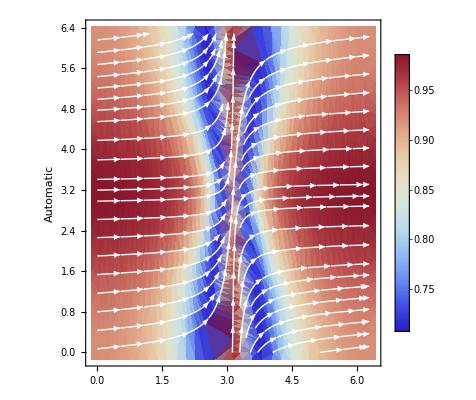

```mathematica
StreamDensityPlot[{P2DefQuantumNorm,P2CoopQuantumNorm},{θDef,0,2π},{θCoop,0,2π},ColorFunction->"ThermometerColors",PlotLegends->Automatic,AxesLabel->Automatic,StreamStyle->{White, Thick}]
```

```mathematica
(* Evolution of Decision-Makers beliefs to Cooperate towards beliefs to Defect *)
```

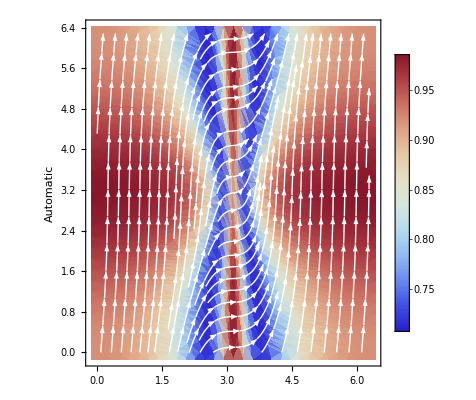

```mathematica
StreamDensityPlot[{P2CoopQuantumNorm,P2DefQuantumNorm},{θDef,0,2π},{θCoop,0,2π},ColorFunction->"ThermometerColors",PlotLegends->Automatic,AxesLabel->Automatic,StreamStyle->{White, Thick}]
```

## Finding the Discrete Wigner Function

The Discrete Wigner function is given by the following formula:
						                                                                    W_α=1/N Tr[ ρ A_α ]

Where
A00=(1 | (1-ⅈ)/2
(1+ⅈ)/2 | 0);         A01=(1 | (-1+ⅈ)/2
(-1-ⅈ)/2 | 0);          A10=(0 | (1+ⅈ)/2
(1-ⅈ)/2 | 1);       A01=(0 | (-1-ⅈ)/2
(-1+ⅈ)/2 | 1);     

According to Wooters (2004), the discrete Wigner function is given by:
                                                                                                                              W=(W_01 | W_11
W_00 | W_10)
 The Pauli Matrices are given by 
                                                                     σ_x=(0 | 1
1 | 0);     σ_y=(0 | -i
i | 0);    σ_z=(1 | 0
0 | -1);

State | State |S⟩ | Density ρ | WignerFunction W
|up⟩ | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (1/2 | 0
1/2 | 0)
|→⟩ | 1/(√2)(1 | 1
1 | 1) | 1/2(1 | 1
1 | 1) | (0 | 0
1/2 | 1/2)
+1 eigenstate
of σ_y | (0 | -i
i | 0) | 1/2(1 | -i
i | 1) | (0 | 1/2
1/2 | 0)
-1 eigenstate
of (σ_x+σ_y+σ_z)/(√3) | 1/(√3)(1 | -2
4 | -1) | (2/3 | 1_6+(√7)/6 ⅈ
1_6-(√7)/6 ⅈ | 1/3) | (0.394 | 0.394
−0.183 | 0.394)

```mathematica
(* Specifying the A matrices *)
```

```mathematica
A00 = ({{1, (1-ⅈ)/2}, {(1+ⅈ)/2, 0}});     A01 = ({{1, (-1+ⅈ)/2}, {(-1-ⅈ)/2, 0}});     A10 = ({{0, (1+ⅈ)/2}, {(1-ⅈ)/2, 1}});     A11 = ({{0, (-1-ⅈ)/2}, {(-1+ⅈ)/2, 1}});
```

```mathematica
(* Specifying the Pauli Matrices *)
```

```mathematica
σx = ({{1, (1-ⅈ)/2}, {(1+ⅈ)/2, 0}});                         σy = ({{1, (-1+ⅈ)/2}, {(-1-ⅈ)/2, 0}});                        σz = ({{0, (1+ⅈ)/2}, {(1-ⅈ)/2, 1}});
```

#### Checking the Computed Discrete Wigner Function

```mathematica
W[ρ_,A_]:= 1/2 Tr[ρ.A];
```

```mathematica
DiscreteWignerF[ρ_, A00_,A01_,A10_,A11_]:= {{W[ρ, A00], W[ρ,A10]},{W[ρ, A01],W[ρ, A11]}};
```

```mathematica
(* Cheking Spin up state *)
```

```mathematica
ρw = ({{1, 0}, {0, 0}});
MatrixForm[DiscreteWignerF[ρw,A01,A00,A11,A10]]
```

(1/2 | 0
1/2 | 0)

```mathematica
(* Cheking |->⟩ state *)
```

```mathematica
ρw = ({{1/2, 1/2}, {1/2, 1/2}});
MatrixForm[DiscreteWignerF[ρw,A01,A00,A11,A10]]
```

(0 | 0
1/2 | 1/2)

```mathematica
(* Cheking +1 Eigenstate of σy *)
```

```mathematica
ρw = ({{1/2, -ⅈ/2}, {ⅈ/2, 1/2}});
MatrixForm[DiscreteWignerF[ρw,A01,A00,A11,A10]]
```

(0 | 1/2
1/2 | 0)

```mathematica
(* Cheking -1 Eigenstate of (σx+σy+σz)/sqrt(3) *)
```

```mathematica
ρw =({{2/3, 1/6+(√7)/6 ⅈ}, {1/6-(√7)/6 ⅈ, 1/3}});
MatrixForm[FullSimplify[DiscreteWignerF[ρw,A01,A00,A11,A10]]]
```

(0.470479 | -0.137146
0.196187 | 0.470479)

### Application of Wooters Discrete Wigner Function

```mathematica
MatrixForm[ρ]
```

(0.485 | 0.0852936 ⅇ^(ⅈ (Re[θ1]-1. Re[θ2])) | 0.451331 ⅇ^(ⅈ (Re[θ1]-1. Re[θ3])) | 0.196977 ⅇ^(ⅈ (Re[θ1]-1. Re[θ4]))
0.0852936 ⅇ^(-ⅈ (Re[θ1]-1. Re[θ2])) | 0.015 | 0.0793725 ⅇ^(ⅈ (Re[θ2]-1. Re[θ3])) | 0.034641 ⅇ^(ⅈ (Re[θ2]-1. Re[θ4]))
0.451331 ⅇ^(-ⅈ (Re[θ1]-1. Re[θ3])) | 0.0793725 ⅇ^(-ⅈ (Re[θ2]-1. Re[θ3])) | 0.42 | 0.183303 ⅇ^(ⅈ (Re[θ3]-1. Re[θ4]))
0.196977 ⅇ^(-ⅈ (Re[θ1]-1. Re[θ4])) | 0.034641 ⅇ^(-ⅈ (Re[θ2]-1. Re[θ4])) | 0.183303 ⅇ^(-ⅈ (Re[θ3]-1. Re[θ4])) | 0.08)

```mathematica
ρw = PartialTrace[ρ,{1}];
MatrixForm[ρw ]
```

(0.905 | 0.0852936 ⅇ^(ⅈ (Re[θ1]-1. Re[θ2]))+0.183303 ⅇ^(ⅈ (Re[θ3]-1. Re[θ4]))
0.0852936 ⅇ^(-ⅈ (Re[θ1]-1. Re[θ2]))+0.183303 ⅇ^(-ⅈ (Re[θ3]-1. Re[θ4])) | 0.095)

```mathematica
pwSimp = FullSimplify[DiscreteWignerF[ρw,A01,A00,A11,A10],{θDef == Re[θ1]-1. Re[θ2], θCoop == Re[θ3]-1. Re[θ4]}];
MatrixForm[pwSimp ]
```

(0.4525-0.0426468 Cos[Re[θ1]-1. Re[θ2]]-0.0916515 Cos[Re[θ3]-1. Re[θ4]]+0.0426468 Sin[Re[θ1]-1. Re[θ2]]+0.0916515 Sin[Re[θ3]-1. Re[θ4]] | 0.0475-0.0426468 Cos[Re[θ1]-1. Re[θ2]]-0.0916515 Cos[Re[θ3]-1. Re[θ4]]-0.0426468 Sin[Re[θ1]-1. Re[θ2]]-0.0916515 Sin[Re[θ3]-1. Re[θ4]]
0.4525+0.0426468 Cos[Re[θ1]-1. Re[θ2]]+0.0916515 Cos[Re[θ3]-1. Re[θ4]]-0.0426468 Sin[Re[θ1]-1. Re[θ2]]-0.0916515 Sin[Re[θ3]-1. Re[θ4]] | 0.0475+0.0426468 Cos[Re[θ1]-1. Re[θ2]]+0.0916515 Cos[Re[θ3]-1. Re[θ4]]+0.0426468 Sin[Re[θ1]-1. Re[θ2]]+0.0916515 Sin[Re[θ3]-1. Re[θ4]])

```mathematica
pwSimp=({{0.4525-0.04264680527307998 Cos[Re[θDef]]-0.09165151389911683 Cos[Re[θCoop]]+0.04264680527307998 Sin[Re[θDef]]+0.09165151389911683 Sin[Re[θCoop]], 0.0475-0.04264680527307998 Cos[Re[θDef]]-0.09165151389911683 Cos[Re[θCoop]]-0.04264680527307998 Sin[Re[θDef]]-0.09165151389911683 Sin[Re[θCoop]]}, {0.4525+0.04264680527307998 Cos[Re[θDef]]+0.09165151389911683 Cos[Re[θCoop]]-0.04264680527307998 Sin[Re[θDef]]-0.09165151389911683 Sin[Re[θCoop]], 0.0475+0.04264680527307998 Cos[Re[θDef]]+0.09165151389911683 Cos[Re[θCoop]]+0.04264680527307998 Sin[Re[θDef]]+0.09165151389911683 Sin[Re[θCoop]]}});
```

```mathematica
(* Color codes: AtlanticColors, BlueGreenYellow, DarkRainbow, PlumColors,SouthwestColors, StarryNightColors, RedBlueTones *)
```

```mathematica
(* Checking W00 *)
```

```mathematica
val1 = 1; val2 = 1;
```

```mathematica
colourFunc = "BlueGreenYellow";
```

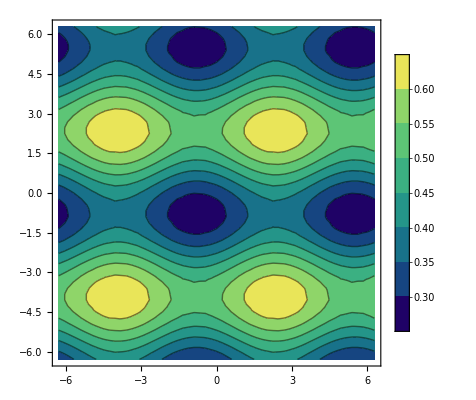
{-Graphics-,-Graphics3D-,-Graphics3D-}

```mathematica
plot00 =Plot3D[{pwSimp[[val1,val2]]},{θDef,-2π,2π},{θCoop,-2π,2π},ColorFunction->(ColorData[colourFunc][#3]&),AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi},{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],Mesh->None];

count00 = ContourPlot[{pwSimp[[val1,val2]] },{θDef,-2π,2π},{θCoop,-2π,2π},PlotLegends->True, ColorFunction->colourFunc];

discr00 = DiscretePlot3D[pwSimp[[val1,val2]],{θDef,-2π,2π},{θCoop,-2π,2π},ExtentSize->Full,Boxed->False,AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]}, Boxed->False,Ticks->{{-2 Pi, -3Pi/2, -Pi,- Pi/2, 0,Pi/2,Pi,3Pi/2,2 Pi},{-2 Pi, -3Pi/2, -Pi, -Pi/2, 0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12], PlotRange->All,ColorFunction->colourFunc,Axes->{True,True,False},PlotLegends->True];
{count00,discr00, plot00}
```

```mathematica
regPlot00 =RegionPlot[{pwSimp[[val1,val2]] < 0},{θDef,-2π,2π},{θCoop,-2π,2π},ColorFunction->(ColorData["BlueGreenYellow"][#3]&),AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]},BoundaryStyle->Thick,Ticks->{{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi},{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],Mesh->None, Axes->{True,True}]
```

-Graphics-

```mathematica
(* Checking W01 *)
```

```mathematica
val1 = 1; val2 = 2;
```

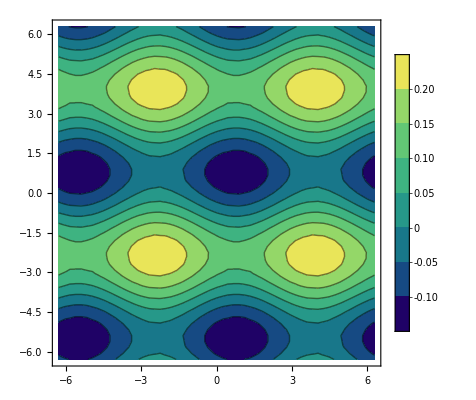
{-Graphics-,-Graphics3D-,-Graphics3D-}

```mathematica
plot01 =Plot3D[{pwSimp[[val1,val2]]},{θDef,-2π,2π},{θCoop,-2π,2π},ColorFunction->(ColorData[colourFunc][#3]&),AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi},{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],Mesh->None];

count01 = ContourPlot[pwSimp[[val1,val2]],{θDef,-2π,2π},{θCoop,-2π,2π},PlotLegends->True, ColorFunction->colourFunc];

discr01 = DiscretePlot3D[pwSimp[[val1,val2]],{θDef,-2π,2π},{θCoop,-2π,2π},ExtentSize->Full,Boxed->False,AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]}, Boxed->False,Ticks->{{-2 Pi, -3Pi/2, -Pi,- Pi/2, 0,Pi/2,Pi,3Pi/2,2 Pi},{-2 Pi, -3Pi/2, -Pi, -Pi/2, 0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12], PlotRange->All,ColorFunction->colourFunc,Axes->{True,True,False},PlotLegends->True];
{count01, discr01, plot01}
```

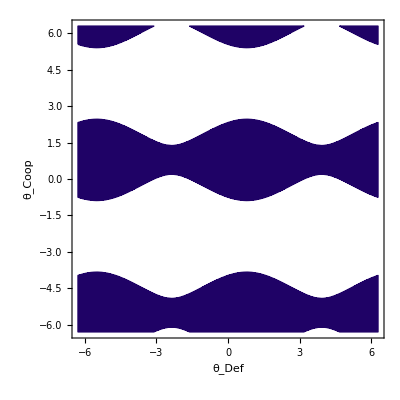

```mathematica
regPlot01 =RegionPlot[{pwSimp[[val1,val2]] < 0},{θDef,-2π,2π},{θCoop,-2π,2π},ColorFunction->(ColorData["BlueGreenYellow"][#3]&),AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]},BoundaryStyle->Thick,Ticks->{{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi},{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],Mesh->None, Axes->{True,True}]
```

```mathematica
(* Checking W10 *)
```

```mathematica
val1 = 2; val2 = 1;
```

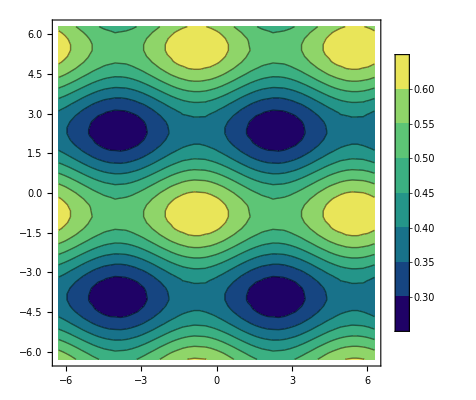
{-Graphics-,-Graphics3D-,-Graphics3D-}

```mathematica
plot10 =Plot3D[{pwSimp[[val1,val2]]},{θDef,-2π,2π},{θCoop,-2π,2π},ColorFunction->(ColorData[colourFunc][#3]&),AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi},{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],Mesh->None];

count10 = ContourPlot[pwSimp[[val1,val2]],{θDef,-2π,2π},{θCoop,-2π,2π},PlotLegends->True, ColorFunction->colourFunc];

discr10 = DiscretePlot3D[pwSimp[[val1,val2]],{θDef,-2π,2π},{θCoop,-2π,2π},ExtentSize->Full,Boxed->False,AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]}, Boxed->False,Ticks->{{-2 Pi, -3Pi/2, -Pi,- Pi/2, 0,Pi/2,Pi,3Pi/2,2 Pi},{-2 Pi, -3Pi/2, -Pi, -Pi/2, 0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12], PlotRange->All,ColorFunction->colourFunc,Axes->{True,True,False},PlotLegends->True];
{count10, discr10, plot10}
```

```mathematica
regPlot10 =RegionPlot[{pwSimp[[val1,val2]] < 0},{θDef,-2π,2π},{θCoop,-2π,2π},ColorFunction->(ColorData["BlueGreenYellow"][#3]&),AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]},BoundaryStyle->Thick,Ticks->{{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi},{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],Mesh->None, Axes->{True,True}]
```

-Graphics-

```mathematica
(* Checking W11 *)
```

```mathematica
val1 = 2; val2 = 2;
```

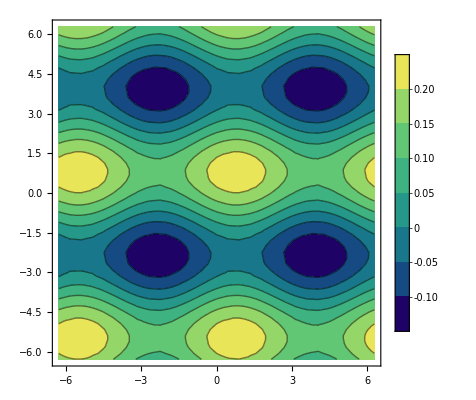
{-Graphics-,-Graphics3D-,-Graphics3D-}

```mathematica
plot11 =Plot3D[{pwSimp[[val1,val2]]},{θDef,-2π,2π},{θCoop,-2π,2π},ColorFunction->(ColorData[colourFunc][#3]&),AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi},{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],Mesh->None];

count11 = ContourPlot[pwSimp[[val1,val2]],{θDef,-2π,2π},{θCoop,-2π,2π},PlotLegends->True, ColorFunction->colourFunc];

discr11 = DiscretePlot3D[pwSimp[[val1,val2]],{θDef,-2π,2π},{θCoop,-2π,2π},ExtentSize->Full,Boxed->False,AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]}, Boxed->False,Ticks->{{-2 Pi, -3Pi/2, -Pi,- Pi/2, 0,Pi/2,Pi,3Pi/2,2 Pi},{-2 Pi, -3Pi/2, -Pi, -Pi/2, 0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12], PlotRange->All,ColorFunction->colourFunc,Axes->{True,True,False},PlotLegends->True];
{count11, discr11, plot11}
```

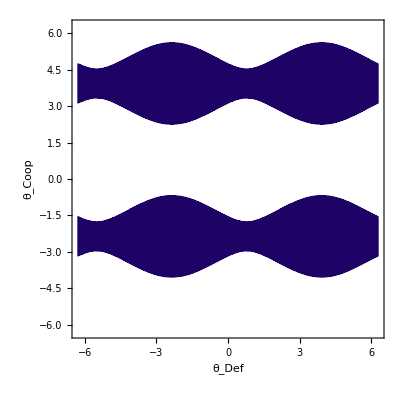

```mathematica
regPlot11 =RegionPlot[{pwSimp[[val1,val2]] < 0},{θDef,-2π,2π},{θCoop,-2π,2π},ColorFunction->(ColorData["BlueGreenYellow"][#3]&),AxesLabel->{Style["θ_Def",16],Style["θ_Coop",16],Style["Prob",16]},BoundaryStyle->Thick,Ticks->{{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi},{-2 Pi, -3Pi/2, -Pi,- Pi/2,0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],Mesh->None, Axes->{True,True}]
```

```mathematica
(*pts={{2.8151,2.8151},{-2.8151,2.8151},{2.8151,-2.8151},{-2.8151,-2.8151}};*)
```